```mathematica
s1 = 0.8;(*saturation parameter 397*)
s2 = 10; (*saturation parameter 866*)
```

```mathematica
H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});
H1=H/.{Subscript[Δ, g]->-10,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2}
```

{{-10,6.47002,0},{6.47002,0,1.72177},{0,1.72177,Δ_r}}

```mathematica
Subscript[C, 1]=√(22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];
```

```mathematica
(*Lindblad eqn*)
```

```mathematica
scanred[δ_]:=Module[{r,H=H1/.{Subscript[Δ, r]->δ},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
]
```

```mathematica
scanred[-10]
```

{0.066134,-9.57113×10^-17,0.933866}

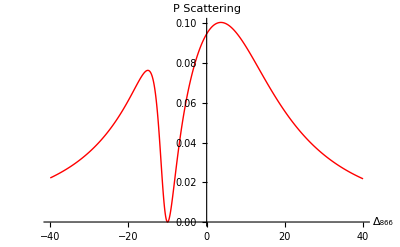

```mathematica
data=Table[{x,scanred[x]},{x,-40,40,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Δ_866","P Scattering"}]
```

```mathematica
foo[30]
```

foo[30]

```mathematica
H2
```

{{Δ_g,6.47002,0},{6.47002,0,1.72177},{0,1.72177,5}}

```mathematica
H2=H/.{Subscript[Δ, r]->5,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2};
scanblue[δ_]:=Module[{r,H=H2/.{Subscript[Δ, g]->δ},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
];

scanblue[-10]
```

{0.576766,0.0998029,0.323431}

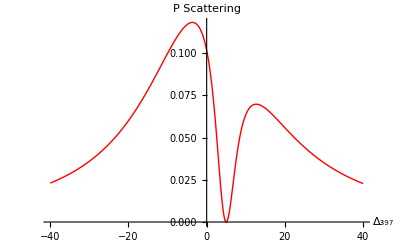

```mathematica
data2=Table[{x,scanblue[x]},{x,-40,40,0.1}];
ListLinePlot[{{data2⟦All,1⟧,data2⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Δ_397","P Scattering"}]
```